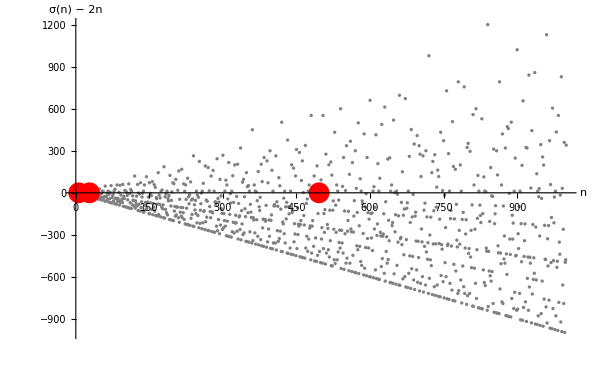

```mathematica
data=Table[{n,DivisorSigma[1,n]-2 n},{n,2,1000}];
perfects={6,28,496};
ListPlot[data,PlotStyle->{Gray,PointSize[0.004]},Epilog->{Red,PointSize[0.025],Point[{#,0}&/@perfects]},AxesLabel->{"n","σ(n) − 2n"},GridLines->{None,{0}},ImageSize->600]
```